# RQA Exploration

Alison Ord

Flip Phillips

## Load FP’s RQA package

```mathematica
gitHubDir=ResourceFunction["NotebookRelativePath"][{"..","..","..","RQA","RQA"}]
```

C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts\..\..\..\RQA\RQA

```mathematica
Get[FileNameJoin[{gitHubDir,"RQA.wl"}]]
```

```mathematica
?RQA`*
```

```mathematica
data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","rock4z.dat"}]]];
```

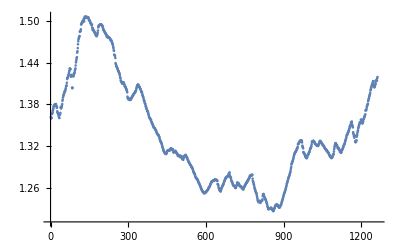

```mathematica
ListPlot[data]
```

```mathematica
ds=RQAMakeTimeSeries[data,1,1]
```

TimeSeries[…]

```mathematica
lag=RQAEstimateLag[ds]
```

305.726

```mathematica
lag=20
```

20

```mathematica
RQAEstimateDimensionality[ds,lag]
```

4.72984×10^-7

{Null,{{{2,0.362319,1262,4.72984×10^-8,1242,1.49292×10^-6},{3,0.0842881,1242,1.49292×10^-6,1222,3.03344×10^-6},{4,0.0166389,1222,3.03344×10^-6,1202,4.40648×10^-6}}}}

```mathematica
embedding=RQAEmbed[ds,3,lag]
```

TimeSeries[…]

```mathematica
ParametricPlot3D[embedding[t],{t,1,650}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222}]
```

-Graphics3D-

```mathematica
rm=RQARecurrenceMap[embedding];
```

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->All]
```

-Graphics-

```mathematica
MinMax[rm]
```

{0,1}

```mathematica
dm=RQADistanceMap[embedding];
```

```mathematica
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All]
```

-Graphics-